## Universal

Check constants and get the inverse function for the discrete distribution.  Start by using integration to obtain the appropriate form for the CDF.

```mathematica
Integrate[1/(x Log[x]^2),x]
```

-1/Log[x]

Need to obtain the normalizing constant.  Normalize for j = 1,2,....  Flip so that subtract so that get the right limit as arguments increase.

```mathematica
Clear[F,f];
Unprotect[K];Clear[K];  K=1/2.10974; Protect[K];
F[j_] :=1-K/Log[j+1];
Finv[p_] := Exp[K/(1-p)]-1;
f[j_] := -K/((j+1)Log[j+1]^2)
```

```mathematica
F[1000000]
Limit[F[n],n->∞]
(* Sum[f[j],{j,1,∞}]  MM cannot solve *)
NSum[f[j],{j,1,∞}]
```

0.965691

1.

-1.

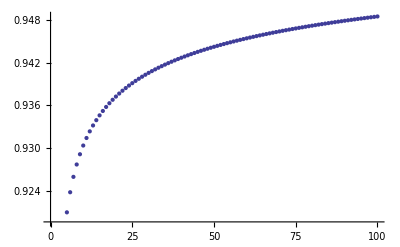

```mathematica
ListPlot[Table[F[j],{j,1,10000,100}]]
```

```mathematica
Finv[F[20]]
F[Finv[0.3]]
```

20.

0.3

## Geometric

Define the geometric density with spending rate ψ and its inverse.  Note that it’s got an ugly inverse function.

```mathematica
Clear[g,K]
g[x_,ψ_]=K+Integrate[-ψ(1-ψ)^(x-1),x]
```

K-((1-ψ)^(-1+x) ψ)/Log[1-ψ]

```mathematica
Clear[h];
h[y_,ψ_]:= 1+(Log[-Log[1-ψ]]-Log[ψ]+Log[y-K])/Log[1-ψ]
```

```mathematica
FullSimplify[h[g[x,ψ],ψ],{x>0,ψ>0, ψ<1}]
```

x

```mathematica
FullSimplify[g[h[x,ψ],ψ],{x>0,ψ>0, ψ<1}]
```

x

For a simpler form, MM pushes terms into the log.

```mathematica
Clear[y,ψ]
FullSimplify[h[y,ψ],{x>0,ψ>0, ψ<1}]
```

Log[-((K-y) (-1+ψ) Log[1-ψ])/ψ]/Log[1-ψ]

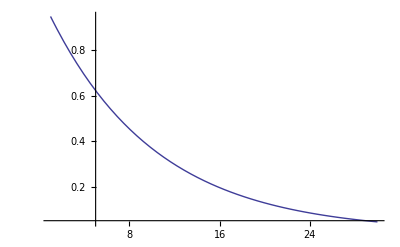

```mathematica
Plot[g[x,0.1],{x,1,30}, PlotRange->All]
```